```mathematica
WindowSpectrogram[data_,sampleRate_,windowSize_,stepSize_]:=Module[{n=Length[data],windows,result,freqs,timeCenters},windows=Table[Take[data,{i,i+windowSize-1}],{i,1,n-windowSize+1,stepSize}];
result=FourierMagnitude/@windows;
freqs=Range[0,Floor[windowSize/2]-1]*sampleRate/windowSize;
result=result[[All, ;;Floor[windowSize/2]]];(*до Nyquist*)timeCenters=Range[1,Length[windows]]*stepSize/sampleRate;(*центр окна*){freqs,timeCenters,Transpose[result]}]

FourierMagnitude[v_]:=2*Abs[Fourier[v,FourierParameters->{1,-1}]]/Length[v];
```

```mathematica
(*Выделим амплитуду сигнала*)values=data[[All,2]];
sampleRate=spec[SampleRate];
```

```mathematica
{freqs,times,spectrogramData}=WindowSpectrogram[values,sampleRate,128,16];
```

```mathematica
ListPlot3D[spectrogramData,DataRange->{{times[[1]],times[[-1]]},{freqs[[1]],freqs[[-1]]}},AxesLabel->{"Time (s)","Frequency (Hz)","Amplitude"},ColorFunction->"SunsetColors",Mesh->None,PlotLabel->"3D Spectrogram"]
```

-Graphics3D-

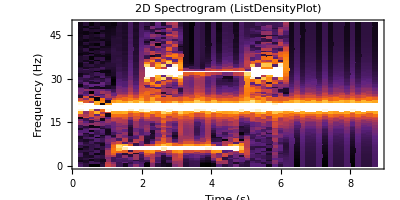

```mathematica
ListDensityPlot[spectrogramData,DataRange->{{times[[1]],times[[-1]]},{freqs[[1]],freqs[[-1]]}},InterpolationOrder->0,ColorFunction->"SunsetColors",FrameLabel->{"Time (s)","Frequency (Hz)"},PlotLabel->"2D Spectrogram (ListDensityPlot)",Frame->True,AspectRatio->1/2,ColorFunctionScaling->True]
```